## Solar Flares & CMEs Problem Set 2 Roy Smart

```mathematica
Clear["Global`*"]
```

## Problem 1

### Part a.

#### Declare the assumptions for this problem

```mathematica
$Assumptions =  λ >0&& z>0 && b > 0  && c >0 && Ics> 0 && h >0 && a>0;
```

#### The flux function for this problem is given by

```mathematica
A[y_,z_] = λ ArcTan[(y+b)/z]-λ ArcTan[(y-b)/z] + Ics/c Log[(y^2 + (z+h)^2)/(y^2+(z-h)^2)];
```

#### Plot this function to ensure that it has the correct behaviour

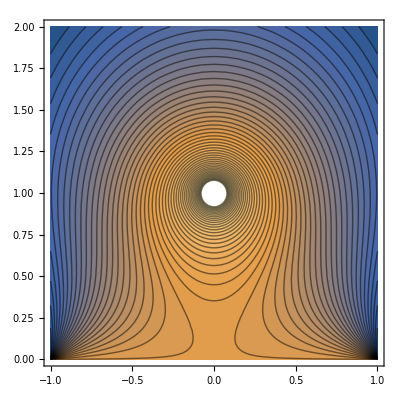

```mathematica
ContourPlot[A[y,z] /. {b-> 1,λ-> 1, h-> 1, Ics-> 0.5, c-> 1},{y,-1,1},{z,0,2},Contours->50]
```

#### The reconnection flux is measured between the origin and the X-point. Find the X-point by setting the magnetic field on the y-axis equal to zero and solve for the height z. Find the magnetic field by taking a curl.

```mathematica
B = Cross[Grad[A[y,z],{x,y,z}],{1,0,0}] /. y->0//FullSimplify
```

{0,(4 h Ics)/(c h^2-c z^2)-(2 b λ)/(b^2+z^2),0}

#### Solve for the height of the X-point

```mathematica
zx = Part[Solve[B[[2]]==0,z] //FullSimplify,2,1,2]
```

√((b h (-2 b Ics+c h λ))/(2 h Ics+b c λ))

#### Expand this solution for a high-lying rope (h >> b)

```mathematica
zxa =Normal[Series[zx  //FullSimplify,{h,Infinity,0}]] /. λ-> 2 Ics /c //FullSimplify
```

√(b h)

#### Plug this expression into the flux function and continue the approximation

```mathematica
(ψr=Series[A[0,zxa],{h,Infinity,1}] /.  λ-> 2 Ics /c//Normal ) //FullSimplify//Framed
```

(8 √(b/h) Ics)/c

### Part b.

#### The measured CME velocity is given as

```mathematica
v = v0/2(Tanh[(t - 2 τ)/τ]+1) /. v0 -> b/τ
```

(b (1+Tanh[(t-2 τ)/τ]))/(2 τ)

#### Height as a function of time is found by performing an indefinite integral over the given velocity

```mathematica
h[t_] =Integrate[v,t] +const
```

const+(b t)/(2 τ)+1/2 b Log[Cosh[(t-2 τ)/τ]]

```mathematica
cv = Part[Solve[h[2τ] ==5b,const],1]
```

{const→4 b}

```mathematica
h[t_] = h[t] /. cv
```

4 b+(b t)/(2 τ)+1/2 b Log[Cosh[(t-2 τ)/τ]]

#### So the flux function becomes

```mathematica
ψ[t_]=ψr /. h-> h[t] /. cv //FullSimplify
```

(8 √2 Ics √(τ/(t+8 τ+τ Log[Cosh[2-t/τ]])))/c

#### Plot the resulting flux function along with the velocity for τ=50sec

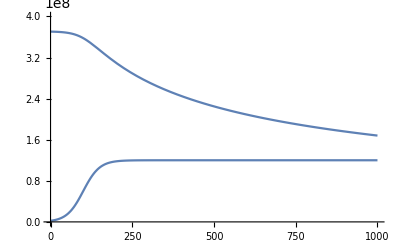

```mathematica
rules50 = {τ-> 50, Ics-> 3 10^21, b-> 6 10^9, c-> 3 10^10};
Plot[{ψ[t]/10^3, v} /. rules50,{t,0,1000},PlotRange->{{0,1000},{0,4 10^8}}]
```

#### Plot the resulting flux function along with the velocity for τ=100sec

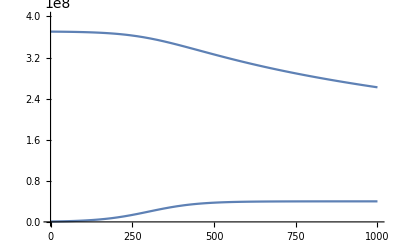

```mathematica
rules150 = {τ-> 150, Ics-> 3 10^21, b-> 6 10^9, c-> 3 10^10};
Plot[{ψ[t]/10^3, v} /. rules150 ,{t,0,1000},PlotRange->{{0,1000},{0,4 10^8}}]
```

### Part c.

#### Find the reconnection rate

```mathematica
dψdt = D[ψ[t],t] //FullSimplify
```

(4 √2 Ics (τ/(t+8 τ+τ Log[Cosh[2-t/τ]]))^(3/2) (-1+Tanh[2-t/τ]))/(c τ)

#### Find the acceleration

```mathematica
ah = D[v,t] //FullSimplify
```

(b Sech[2-t/τ]^2)/(2 τ^2)

#### Plot the reconnection rate and acceleration for τ=50 sec

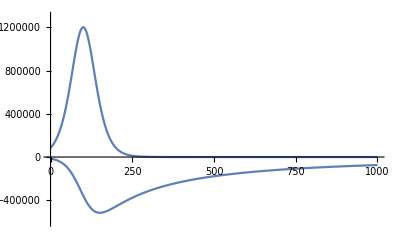

```mathematica
Plot[{dψdt/10^3, ah} /. rules50,{t,0,1000},PlotRange->{{0,1000},{-6 10^5, 1.3 10^6}}]
```

#### Plot the reconnection rate and acceleration for τ=150 sec

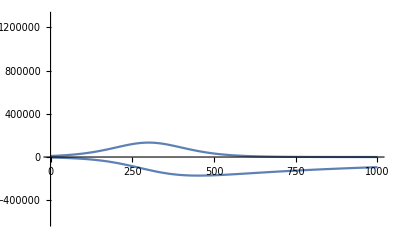

```mathematica
Plot[{dψdt/10^3, ah} /. rules150,{t,0,1000},PlotRange->{{0,1000},{-6 10^5, 1.3 10^6}}]
```

#### Find the time of maximum reconnection rate for τ=50 sec

```mathematica
(dψdtmin50 =Part[FindMinimum[dψdt /.rules50,{t,300}],2,1,2])//Framed
```

150.843

#### Find the time of maximum acceleration for τ=50 sec

```mathematica
(ahmax50 =Part[FindMaximum[ah /.rules50,{t,100}] //Quiet,2,1,2])//Framed
```

100.

#### Find the time of maximum reconnection rate for τ=150 sec

```mathematica
(dψdtmin150 =Part[FindMinimum[dψdt /.rules150,{t,300}],2,1,2])//Framed
```

452.528

#### Find the time of maximum acceleration for τ=150 sec

```mathematica
(ahmax150 =Part[FindMaximum[ah /.rules150,{t,100}] //Quiet,2,1,2])//Framed
```

300.

### Part d.

#### Express the volume in terms of an initial volume V0 and a change in volume ΔV

```mathematica
V=V0+ΔV;
```

#### Denote the initial volume in terms of an area a and length L

```mathematica
V0 =a h0
```

a h0

#### The change in volume is said to be proportional to the height h

```mathematica
ΔV = a (h - h0);
```

#### The number density is the number of particles over volume

```mathematica
n= N/V;
n0 = N/V0;
```

#### The ratio of the number density to the initial number density is then

```mathematica
(nR=n/n0 //FullSimplify)//Framed
```

h0/h

#### Plot this ratio as a function of time

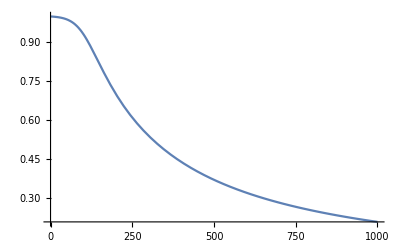

```mathematica
Plot[nR /. {h-> h[t],h0-> h[0], L-> 1, α->1} /. rules50,{t,0,1000}]
```

#### The temperature is given by the adiabatic process

```mathematica
γ=5/3;
T = β/V^(γ-1);
T0 = β/V0^(γ-1);
```

#### The ratio of the temperature to the initial temperature is then

```mathematica
(TR=T/T0 //FullSimplify) //Framed
```

(h0/h)^(2/3)

#### Plot this ratio as a function of time

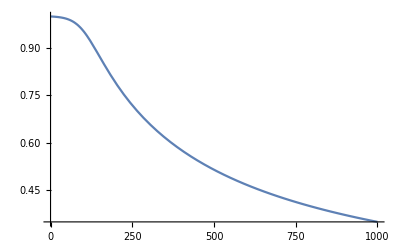

```mathematica
Plot[TR /. {h-> h[t],h0-> h[0], L-> 1} /. rules50,{t,0,1000}]
```

#### The emission measure is the square of the number density integrated over the length of the axial flux tube

```mathematica
EM = n^2 h //FullSimplify
EM0 = n0^2 h0 //FullSimplify
```

N^2/(a^2 h)

N^2/(a^2 h0)

#### The ratio of the initial emission measure to the final emission measure is then

```mathematica
(EMR=EM/EM0 //FullSimplify)//Framed
```

h0/h

#### and the plot of this ratio is

```mathematica
Plot[EMR /. {h-> h[t],h0-> h[0], L-> 1} /. rules50,{t,0,1000}]
```

-Graphics-

### Part e.

#### The response function for our instrument is given as

```mathematica
G[T_]:=Exp[-(T-T00)^2/(2 Tw^2)]
```

#### Evaluate at current temperature

```mathematica
GR = G[TR T00] /. T00 -> 2 Tw //FullSimplify
```

ⅇ^(-2 (-1+(h0/h)^(2/3))^2)

#### Plot the counts, which is the product of the temperature sensitivity and the emission measure

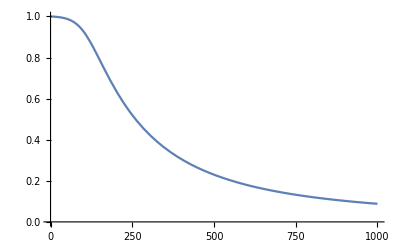

```mathematica
Plot[GR EMR/.{h-> h[t],h0-> h[0],L-> 1} /. rules50,{t,0,1000}]
```

#### Evaluate the extent of dimming when the flux rope is twice the initial height

```mathematica
GR EMR /.h-> 2h[0] /.h0-> h[0]//FullSimplify //Framed
```

1/2 ⅇ^(-2 (-1+1/2^(2/3))^2)